# Tutorial: Using the Osculating Orbital Elements Package

## Importing the Package

The package is imported using the following command. This package requires the KerrGeodesics Package, which can be found at github.com/BlackHolePerturbationToolkit/KerrGeodesics

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oleksii/MEGA/OsculatingOrbitalElements

```mathematica
<<OsculatingOrbitalElements`
```

SetDirectory::cdir: Cannot set current directory to /Users/oleksii/Library/Wolfram/Applications/OsculatingOrbitalElements/DataFiles.

Import::nffil: File a_n_jk not found during Import.

Import::nffil: File b_n_jk not found during Import.

Import::nffil: File c_n_jk not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["/home/oleksii/.Wolfram/Applications/OsculatingOrbitalElements-master/OsculatingOrbitalElements.m"]
```

SetDirectory::cdir: Cannot set current directory to /home/oleksii/.Wolfram/Applications/OsculatingOrbitalElements/DataFiles.

Import::nffil: File a_n_jk not found during Import.

Import::nffil: File b_n_jk not found during Import.

Import::nffil: File c_n_jk not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

## Schwarzschild Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements first derived in Pound and Poisson[1]. This code adopts the notation used in Warburton et al [2]. 
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum
e is the eccentricity
ξ is the phase variable, defined by ξ = χ - χ_0.
The equations are integrated w.r.t the Darwin Parameter χ.
Fr and Fϕ are contrvarient componets of the acceleration.

#### SchwarzOsculatingOrbitalElements

```mathematica
?SchwarzOsculatingOrbitalElements
```

```mathematica
?SchwarzOsculatingOrbitalElementsTP
```

SchwarzOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

### User Specified Model

First, we are going to define force components for use with SchwarzOsculatingOrbitalElements. These components need to be functions of p, e and ξ.

```mathematica
"Fr"->-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) Sin[ξ],"Fϕ"->-(1+e Cos[ξ])^2/(p √(-3-e^2+p))
```

```mathematica
Fr[p_, e_, ξ_] :=-e Sin[ξ] √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) ;(*Fr[p_, e_, ξ_] :=-e √((-6+p-2 e(p-r)/(e r))/(p (-3-e^2+p)))*)
Fϕ[p_, e_, ξ_] := -(1+e Cos[ξ])^2/(p √(-3-e^2+p));(*Fϕ[p_, e_, ξ_] := -p/(r^2 √(-3-e^2+p))*)
```

Next, we specify the mass ratio along with initial conditions of the orbit.

```mathematica
η=10^-6;
p0=30;
e0=0.9;
ξ0=0;
```

Now we solve the osculating geodesic equations and save the result to the symbol ‘orbit’

```mathematica
orbit = SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$605576,θ→OsculatingOrbitalElements`Private`θsol$605576,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…],limit→398.837|>

```mathematica
orbitT = SchwarzOsculatingOrbitalElementsTP[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$606608,θ→OsculatingOrbitalElements`Private`θsol$606608,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…],limit→404247.|>

The output is an association. You can access these functions using the following syntax:

```mathematica
orbitT["r"][40]
```

12.0429

```mathematica
orbit["r"][1642]
```

7.1101

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimit = orbit["t"]["Domain"][[1,2]]
```

398.837

```mathematica
(orbit["p"][χ])/(√(-3-(orbit["e"][χ])^2+orbit["p"][χ]))
```

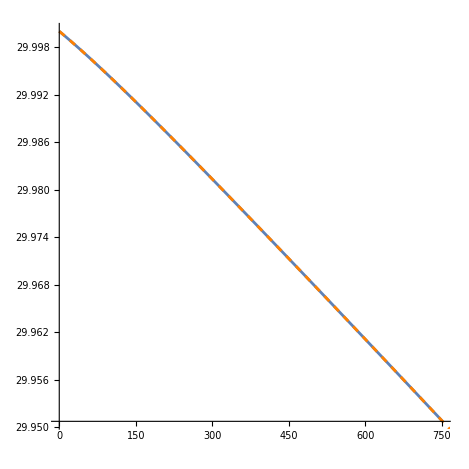

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["p"][χ]}, {χ, 0, 2}, AspectRatio->1],ParametricPlot[{t,orbitT["p"][t]}, {t, 0, 1000}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

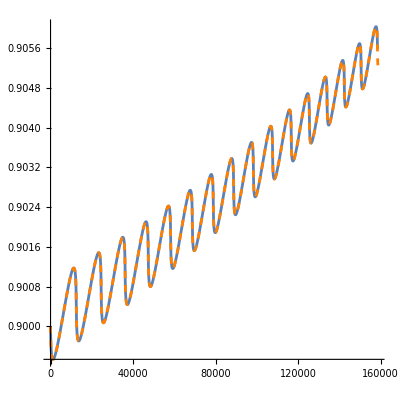

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["e"][χ]}, {χ, 0, 100}, AspectRatio->1],ParametricPlot[{t,orbitT["e"][t]}, {t, 0, 159316}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["e"][χ]}, {χ, 0, 100}, AspectRatio->1],ParametricPlot[{t,orbitT["e"][t]}, {t, 0, 159316}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

-Graphics-

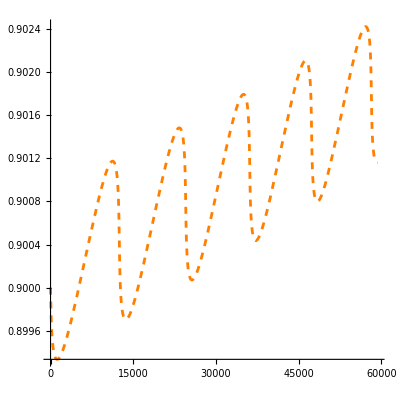

```mathematica
ParametricPlot[{t,orbitT["e"][t]}, {t, 0, 59316}, AspectRatio->1,PlotStyle->{Dashed,Orange}]
```

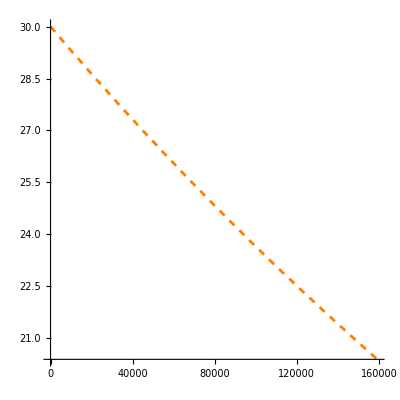

```mathematica
ParametricPlot[{t,orbitT["p"][t]}, {t, 0, 159316}, AspectRatio->1,PlotStyle->{Dashed,Orange}]
```

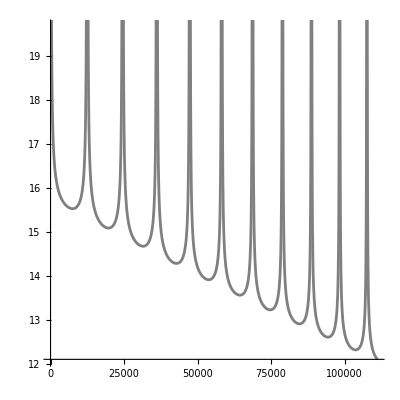

```mathematica
ParametricPlot[{t,orbitT["r"][t]}, {t, 0,111200}, AspectRatio->1,PlotStyle->Gray]
```

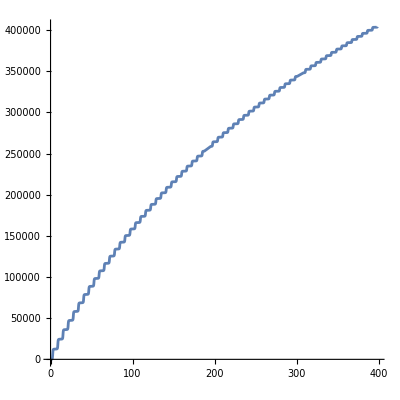

```mathematica
Plot[{orbit["t"][χ]}, {χ, 0, plotLimit}, AspectRatio->1]
```

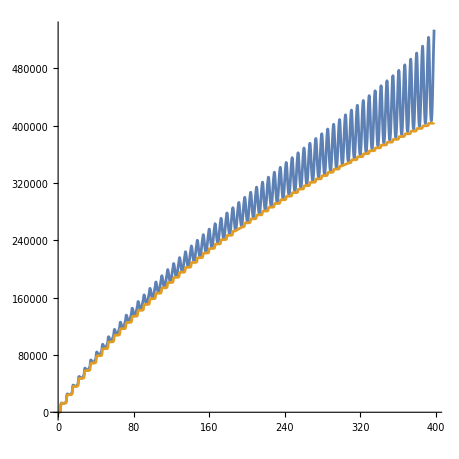

```mathematica
Plot[{orbit["t"][χ]/(1-1/orbit["r"][χ]),orbit["t"][χ]}, {χ, 0, plotLimit}, AspectRatio->1]
```

```mathematica
?Disk
```

```mathematica
phi[χ_]:=NIntegrate[p0^(1/2)/Sqrt[p0-6-2 e0 Cos[xi-ξ0]],{xi,0,χ}]
```

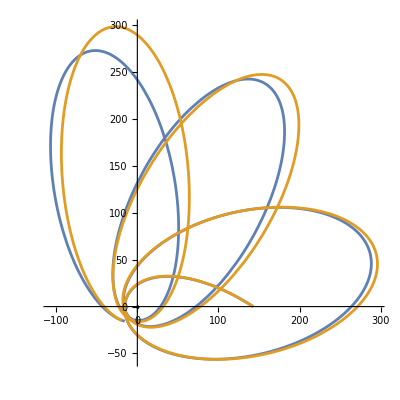

```mathematica
Show[ParametricPlot[{{orbit["r"][χ]Cos[orbit["ϕ"][χ]], orbit["r"][χ]Sin[orbit["ϕ"][χ]]},{p0/(1-e0 Cos[χ+ξ0]) Cos[phi[χ]], p0/(1-e0 Cos[χ+ξ0])Sin[phi[χ]]}}, {χ,0, 2 10.1}, AspectRatio->1,PlotRange->All],{Graphics[Disk[{0,0},2]]}]
```

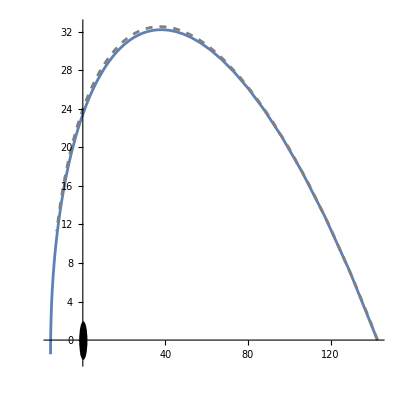

```mathematica
Show[ParametricPlot[{{orbitT["r"][t]Cos[orbitT["ϕ"][t]], orbitT["r"][t]Sin[orbitT["ϕ"][t]]}}, {t,0, 10000}, AspectRatio->1,PlotRange->All],Graphics[Disk[{0,0},2]],ParametricPlot[{{p0/(1-e0 Cos[χ+ξ0]) Cos[phi[χ]], p0/(1-e0 Cos[χ+ξ0])Sin[phi[χ]]}}, {χ,0, 2.1}, AspectRatio->1,PlotStyle->{Gray,Dashed}]]
```

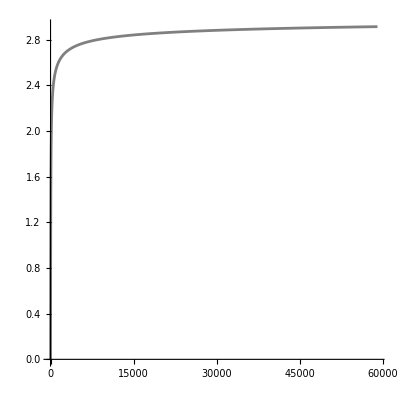

```mathematica
ParametricPlot[{t,orbitT["ϕ"][t]}, {t, 0, 59000}, AspectRatio->1,PlotStyle->Gray,PlotRange->All]
```

### Included Models

#### SchwarzGasDrag

Not specifying a Force option means that SchwarzOsculatingOrbitalElements uses the SchwarzGasDrag model.

```mathematica
?SchwarzGasDrag
```

```mathematica
SchwarzGasDrag[p, e, ξ]
```

<|Fr→-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) Sin[ξ],Fϕ→-(1+e Cos[ξ])^2/(p √(-3-e^2+p))|>

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10293,θ→OsculatingOrbitalElements`Private`θsol$10293,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

One can also specify this option explicitly.

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzGasDrag]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10843,θ→OsculatingOrbitalElements`Private`θsol$10843,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

#### SchwarzFastGSF

One can also choose to use SchwarzFastGSF model. Note that this model is valid for p <= 12 and e<= 0.2.

```mathematica
?SchwarzFastGSF
```

```mathematica
SchwarzFastGSF[p,e,ξ]
```

Part::partd: Part specification $Failed⟦4,3;;12⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦4,14;;23⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦4,25;;34⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of $Failed⟦4,3;;12⟧ does not exist.

Part::partw: Part 5 of $Failed⟦4,3;;12⟧ does not exist.

Part::partw: Part 6 of $Failed⟦4,3;;12⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzFastGSF]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[{{0., 474691.}}, <>],r→OsculatingOrbitalElements`Private`rsol$12936,θ→OsculatingOrbitalElements`Private`θsol$12936,ϕ→InterpolatingFunction[{{0., 474691.}}, <>],p→InterpolatingFunction[{{0., 474691.}}, <>],e→InterpolatingFunction[{{0., 474691.}}, <>],ξ→InterpolatingFunction[{{0., 474691.}}, <>]|>

## Kerr Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements for Kerr first derived in Gair et al [3] and uses the notation given in that paper.
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum.
e is the eccentricity.
x is Cos[θinc].
En is orbital energy.
L angular momentum about the symmetry axis.
K is the modified Carter Constant defined by K = Q + (L - a (En))^2
ψr is the radial phase variable.
ψθ is the polar phase variable.
The equations are integrated w.r.t Mino time λ.
at, ar, aθ, aϕ are covariant components of the acceleration.

#### KerrOsculatingOrbitalElements

```mathematica
?KerrOsculatingOrbitalElements
```

```mathematica
?KerrOsculatingOrbitalElementsTP
```

KerrOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

### User Specified Model

First, we are going to define force components for use with KerrOsculatingOrbitalElements. These components need to be functions of En, L, K, ψr and ψθ. We’re just going to use the KerrGasDrag model for this example

```mathematica
at[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["at"];
ar[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["ar"];
aθ[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aθ"];
aϕ[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aϕ"];
```

```mathematica
ft[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["ft"];
fr[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fr"];
fθ[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fθ"];
fϕ[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fϕ"];
```

Next, we specify the mass ratio, the spin and the initial conditions of the orbit.

```mathematica
η = 10^-5;
a0 = 0.9;
p0 = 7;
e0 = 0.01;
x0 = Cos[π/6];
ψr0 = 0;
ψθ0 =0;
```

Now we solve the osculating geodesic equations and save the result to the symbol ‘kerrOrbit’

```mathematica
kerrOrbit = KerrOsculatingOrbitalElements[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {at,ar,aθ,aϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$21963,θ→OsculatingOrbitalElements`Private`θsol$21963,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$21963,p→OsculatingOrbitalElements`Private`psol$21963,e→OsculatingOrbitalElements`Private`esol$21963,x→OsculatingOrbitalElements`Private`xsol$21963,ι→OsculatingOrbitalElements`Private`ιsol$21963,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$21963,r2→OsculatingOrbitalElements`Private`r2sol$21963,z1→OsculatingOrbitalElements`Private`zmsol$21963,limit→1371.63|>

The output is an association. You can access these functions using the following syntax:

```mathematica
kerrOrbitGeod = KerrOsculatingOrbitalElements[0,a0, p0, e0, x0, ψr0, ψθ0, Force -> {at,ar,aθ,aϕ}]
```

Starting NDSolve...

```mathematica
kerrOrbitGeod1 = KerrGeoOrbit[a0, p0, e0, x0]
```

KerrGeoOrbitFunction[…]

```mathematica
kerrOrbitTP = KerrOsculatingOrbitalElementsTP[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {at,ar,aθ,aϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$23082,θ→OsculatingOrbitalElements`Private`θsol$23082,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$23082,p→OsculatingOrbitalElements`Private`psol$23082,e→OsculatingOrbitalElements`Private`esol$23082,x→OsculatingOrbitalElements`Private`xsol$23082,ι→OsculatingOrbitalElements`Private`ιsol$23082,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$23082,r2→OsculatingOrbitalElements`Private`r2sol$23082,z1→OsculatingOrbitalElements`Private`zmsol$23082,limit→41604.3|>

```mathematica
<<OsculatingOrbitalElements`
```

SetDirectory::cdir: Cannot set current directory to /Users/oleksii/Library/Wolfram/Applications/OsculatingOrbitalElements/DataFiles.

Import::nffil: File a_n_jk not found during Import.

Import::nffil: File b_n_jk not found during Import.

Import::nffil: File c_n_jk not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
kerrOrbitTPVec = KerrOsculatingOrbitalElementsTPVec[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {ft,fr,fθ,fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$22333,θ→OsculatingOrbitalElements`Private`θsol$22333,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$22333,p→OsculatingOrbitalElements`Private`psol$22333,e→OsculatingOrbitalElements`Private`esol$22333,x→OsculatingOrbitalElements`Private`xsol$22333,ι→OsculatingOrbitalElements`Private`ιsol$22333,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$22333,r2→OsculatingOrbitalElements`Private`r2sol$22333,z1→OsculatingOrbitalElements`Private`zmsol$22333,limit→41604.3|>

```mathematica
kerrOrbitTPVecLessArg = KerrOsculatingOrbitalElementsTPVecLessArg[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {fr,fθ,fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$23453,θ→OsculatingOrbitalElements`Private`θsol$23453,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$23453,p→OsculatingOrbitalElements`Private`psol$23453,e→OsculatingOrbitalElements`Private`esol$23453,x→OsculatingOrbitalElements`Private`xsol$23453,ι→OsculatingOrbitalElements`Private`ιsol$23453,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$23453,r2→OsculatingOrbitalElements`Private`r2sol$23453,z1→OsculatingOrbitalElements`Private`zmsol$23453,limit→41604.3|>

```mathematica
{tgeod,rgeod,θgeod,φgeod}=kerrOrbitGeod1["Trajectory"];
```

```mathematica
kerrOrbit["r"][100]
```

kerrOrbit[r][100]

```mathematica
kerrOrbitTP["r"][100]
```

13.4285

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimit = kerrOrbit["t"]["Domain"][[1,2]]
```

1371.63

```mathematica
plotLimitTP = kerrOrbitTPVecLessArg["ϕ"]["Domain"][[1,2]]
```

41604.3

```mathematica
{kerrOrbitTP["p"][1], kerrOrbitTP["e"][1]}
```

{6.9999,0.499979}

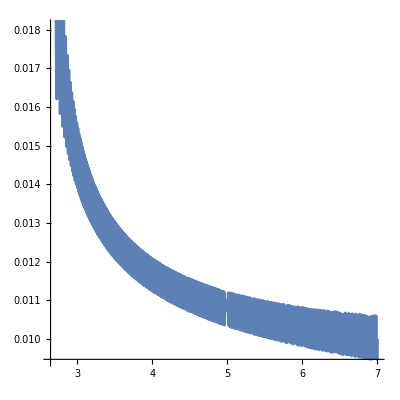

```mathematica
ParametricPlot[{kerrOrbit["p"][χ], kerrOrbit["e"][χ]}, {χ, 0, plotLimit}, AspectRatio->1]
```

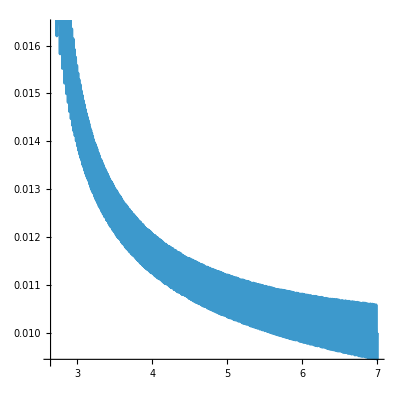

```mathematica
ParametricPlot[{kerrOrbitTP["p"][t], kerrOrbitTP["e"][t]}, {t, 0, plotLimitTP}, AspectRatio->1]
```

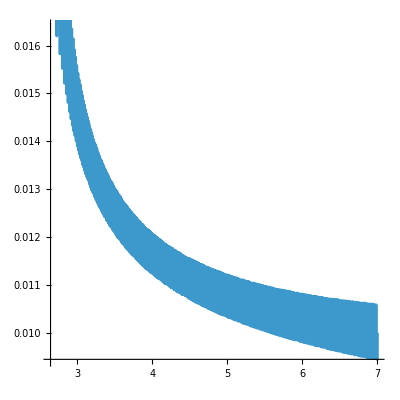

```mathematica
ParametricPlot[{kerrOrbitTPVec["p"][t], kerrOrbitTPVec["e"][t]}, {t, 0, plotLimitTP}, AspectRatio->1]
```

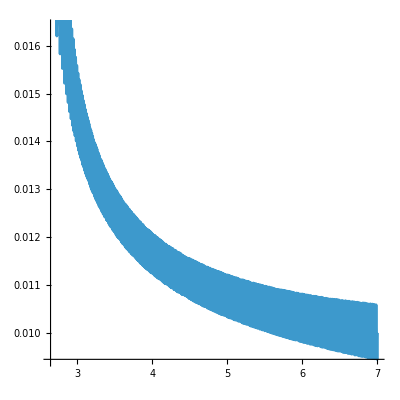

```mathematica
ParametricPlot[{kerrOrbitTPVecLessArg["p"][t], kerrOrbitTPVecLessArg["e"][t]}, {t, 0, plotLimitTP}, AspectRatio->1]
```

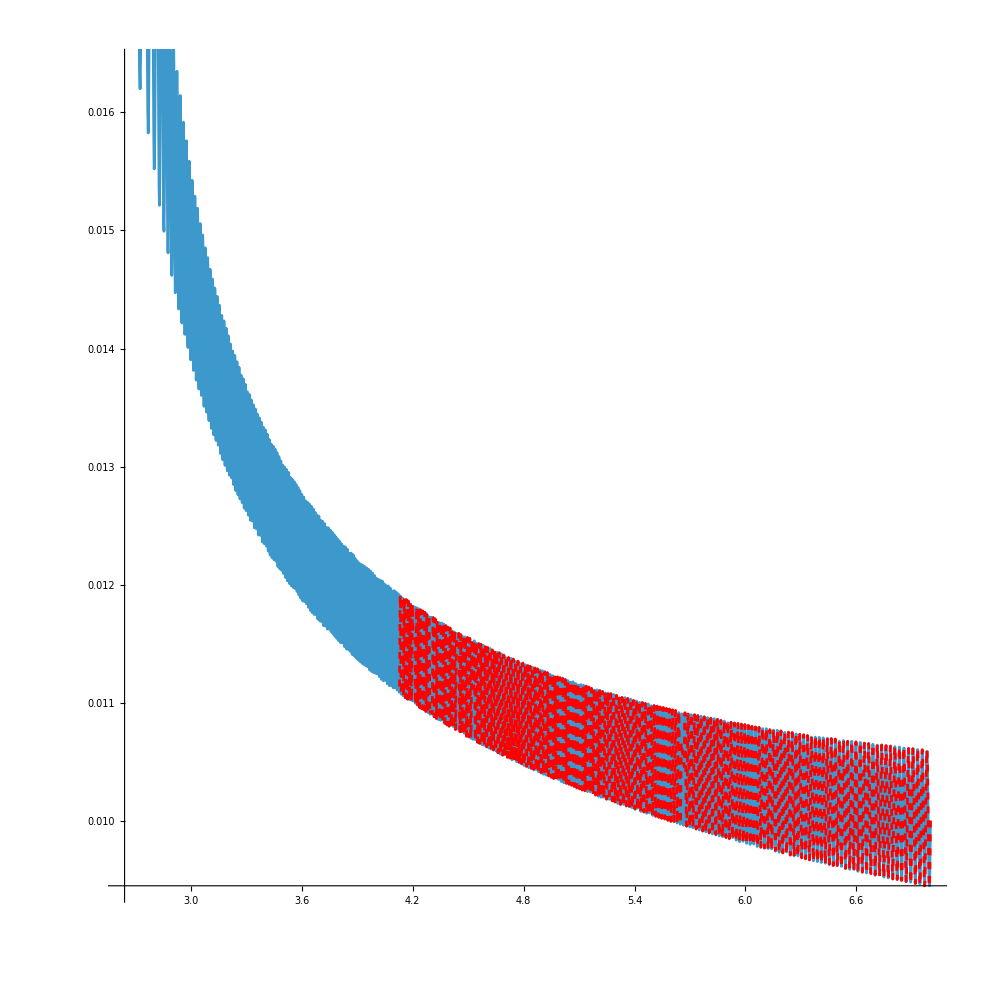

```mathematica
Show[ParametricPlot[{kerrOrbitTPVecLessArg["p"][t], kerrOrbitTPVecLessArg["e"][t]}, {t, 0, plotLimitTP}, AspectRatio->1],ParametricPlot[{kerrOrbitTPVec["p"][t], kerrOrbitTPVec["e"][t]}, {t, 0, 2.6 10^4}, AspectRatio->1,PlotStyle->{Red,Dashed}]]
```

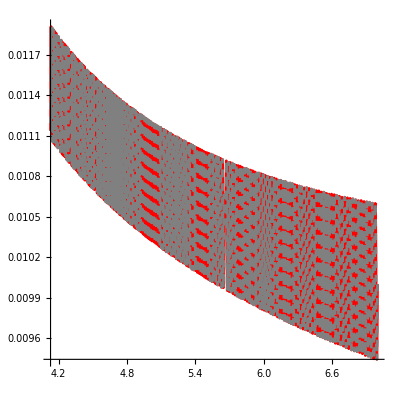

```mathematica
Show[ParametricPlot[{kerrOrbitTP["p"][t], kerrOrbitTP["e"][t]}, {t, 0, 2.6 10^4}, AspectRatio->1,PlotStyle->{Red}],ParametricPlot[{kerrOrbitTPVec["p"][t], kerrOrbitTPVec["e"][t]}, {t, 0, 2.6 10^4}, AspectRatio->1,PlotStyle->{Gray,Dashed}]]
```

```mathematica
ParametricPlot3D[{{kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Sin[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Cos[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Sin[ kerrOrbit["θ"][χ]]},{kerrOrbitGeod["r"][χ]Cos[ kerrOrbitGeod["θ"][χ]]Sin[ kerrOrbitGeod["ϕ"][χ]],kerrOrbitGeod["r"][χ]Cos[ kerrOrbitGeod["θ"][χ]]Cos[ kerrOrbitGeod["ϕ"][χ]],kerrOrbitGeod["r"][χ]Sin[ kerrOrbitGeod["θ"][χ]]}}, {χ, 0, 2Pi}, AspectRatio->1]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Sin[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Cos[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Sin[ kerrOrbit["θ"][χ]]},{kerrOrbitGeod["r"][χ]Cos[ kerrOrbitGeod["θ"][χ]]Sin[ kerrOrbitGeod["ϕ"][χ]],kerrOrbitGeod["r"][χ]Cos[ kerrOrbitGeod["θ"][χ]]Cos[ kerrOrbitGeod["ϕ"][χ]],kerrOrbitGeod["r"][χ]Sin[ kerrOrbitGeod["θ"][χ]]}}, {χ,plotLimit-4Pi, plotLimit}, AspectRatio->1]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Sin[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Cos[ kerrOrbit["θ"][χ]]Cos[ kerrOrbit["ϕ"][χ]],kerrOrbit["r"][χ]Sin[ kerrOrbit["θ"][χ]]},{rgeod[χ]Cos[θgeod[χ]]Sin[ φgeod[χ]],rgeod[χ]Cos[θgeod[χ]]Cos[ φgeod[χ]],rgeod[χ]Sin[ θgeod[χ]]}}, {χ, 0, 2Pi}, AspectRatio->1]
```

-Graphics3D-

```mathematica
rgeod[1]
```

9.66295

### Consistency check: Kerr ⟶ Schwarzschild for small a

```mathematica
a0 = 0.1; 
x0 = Cos[π/2];
ψr0 = 0;
ψθ0 =0;
η=10^-6;
p0=30;
e0=0.9;
ξ0=0;
```

```mathematica
kerrOrbitTPVecLessArg = KerrOsculatingOrbitalElementsTPVecLessArg[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {fr,fθ,fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$867179,θ→OsculatingOrbitalElements`Private`θsol$867179,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$867179,p→OsculatingOrbitalElements`Private`psol$867179,e→OsculatingOrbitalElements`Private`esol$867179,x→OsculatingOrbitalElements`Private`xsol$867179,ι→OsculatingOrbitalElements`Private`ιsol$867179,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$867179,r2→OsculatingOrbitalElements`Private`r2sol$867179,z1→OsculatingOrbitalElements`Private`zmsol$867179,limit→404548.|>

```mathematica
plotLimitTP = kerrOrbitTPVecLessArg["ϕ"]["Domain"][[1,2]]
```

404548.

```mathematica
orbitT = SchwarzOsculatingOrbitalElementsTP[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$867813,θ→OsculatingOrbitalElements`Private`θsol$867813,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…],limit→404247.|>

```mathematica
plotLimitTP =Min[ kerrOrbitTPVecLessArg["ϕ"]["Domain"][[1,2]], orbitT["ϕ"]["Domain"][[1,2]]]
```

404247.

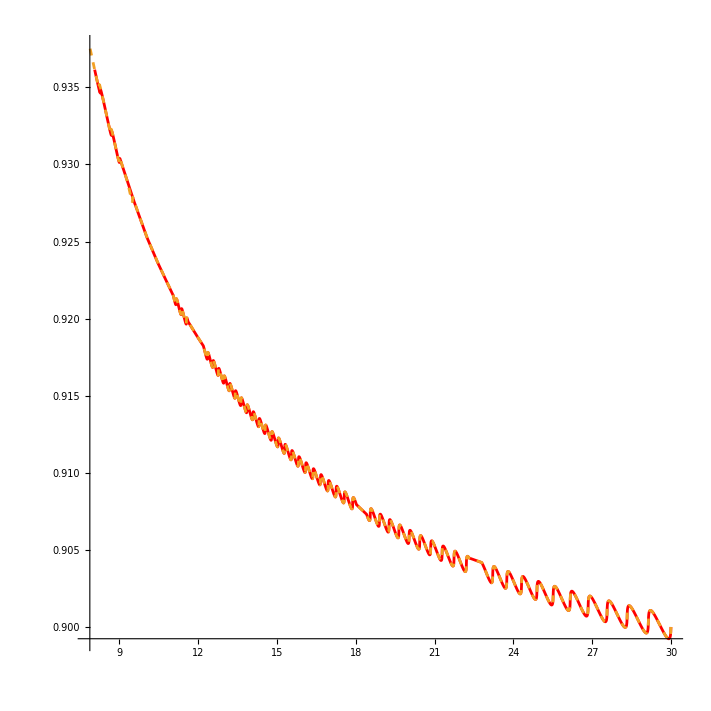

```mathematica
ParametricPlot[{{kerrOrbitTPVecLessArg["p"][t], kerrOrbitTPVecLessArg["e"][t]},{orbitT["p"][t], orbitT["e"][t]}}, {t, 0, plotLimitTP}, AspectRatio->1,PlotStyle->{Red,Dashed}]
```

### Included Models

#### KerrGasDrag

Not specifying a Force option means that KerrOsculatingOrbitalElements uses the KerrGasDrag model.

```mathematica
?KerrGasDrag
```

## References

[1] arxiv.org/abs/0708.3033
[2] arxiv.org/abs/1111.6908
[3] arxiv.org/abs/1012.5111